# 1. kviz - Računalniška orodja v matematiki

Na kvizu je skupno možno doseči 20 točk. Za vsako pravilno rešeno podnalogo dobite 1 točko. Delnih točk ni.
Rešitve pišite takoj pod navodilom ustrezne podnaloge. 

Veliko uspeha pri reševanju!

#### 1. Prepisovalna pravila

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja s klicem funkcije f na argumentu x.

```mathematica
pravilo = {x-> f[x]}
```

b. Na izrazu `izraz` najprej uporabite pravilo definirano v prejšnji nalogi za funkcijo , nato pa s prepisovalnimi pravili izračunajte vrednost dobljenega izraza za x = e (x = ⅇ) in y = 1/2.

```mathematica
izraz = Log[x] + 2y / x; 
f[x_]:= x^4 + 1
izraz /. pravilo
```

(2 y)/x+Log[x]/.2 ⅇ^(-3-x) (2+100 x) y+Log[ⅇ^(3+x)/(2+100 x)]

```mathematica
f[x]/.pravilo
```

ReplaceAll::reps: {2 ⅇ^(-3-x) (2+100 x) y+Log[ⅇ^(3+x)/(2+100 x)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1+x^4/.2 ⅇ^(-3-x) (2+100 x) y+Log[ⅇ^(3+x)/(2+100 x)]

```mathematica
pravilo /. {x -> E, y->1/2}
```

ⅇ^(-3-ⅇ) (2+100 ⅇ)+Log[ⅇ^(3+ⅇ)/(2+100 ⅇ)]

c. Definirajte prepisovalno pravilo, ki zamenja vse pojavitve  z .

```mathematica
novopravilo = {x^n -> Divide[x^(n+1), 2*n+1]}
```

{x^n→x^(1+n)/(1+2 n)}

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_]:= x^(-42)
g[x]/. novopravilo
```

1/x^42

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`.

```mathematica
zac = Fib[10]
zac //. {Fib[0]-> 0, Fib[1]-> 1, Fib[n_]:> Fib[n-1] + Fib[n-2]}
```

Fib[10]

55

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll[x, y, g, n,f]
```

b. Definirajte tabelo, ki bo vsebovala numerične približke naravnega logaritma v vseh številih med 1 in 100.

```mathematica
tabela =Table[N[Log[x]], {x, 1, 100}]
```

{0.,0.693147,1.09861,1.38629,1.60944,1.79176,1.94591,2.07944,2.19722,2.30259,2.3979,2.48491,2.56495,2.63906,2.70805,2.77259,2.83321,2.89037,2.94444,2.99573,3.04452,3.09104,3.13549,3.17805,3.21888,3.2581,3.29584,3.3322,3.3673,3.4012,3.43399,3.46574,3.49651,3.52636,3.55535,3.58352,3.61092,3.63759,3.66356,3.68888,3.71357,3.73767,3.7612,3.78419,3.80666,3.82864,3.85015,3.8712,3.89182,3.91202,3.93183,3.95124,3.97029,3.98898,4.00733,4.02535,4.04305,4.06044,4.07754,4.09434,4.11087,4.12713,4.14313,4.15888,4.17439,4.18965,4.20469,4.21951,4.23411,4.2485,4.26268,4.27667,4.29046,4.30407,4.31749,4.33073,4.34381,4.35671,4.36945,4.38203,4.39445,4.40672,4.41884,4.43082,4.44265,4.45435,4.46591,4.47734,4.48864,4.49981,4.51086,4.52179,4.5326,4.54329,4.55388,4.56435,4.57471,4.58497,4.59512,4.60517}

c.  Iz tabele v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu desetin (prvo decimalno mesto) praštevilo.

```mathematica
seznam = Select[tabela,PrimeQ[IntegerPart[Mod[#*10, 10]]]&]
```

{1.38629,1.79176,2.30259,2.3979,2.56495,2.70805,2.77259,3.21888,3.2581,3.29584,3.3322,3.3673,3.52636,3.55535,3.58352,3.71357,3.73767,3.7612,3.78419,4.20469,4.21951,4.23411,4.2485,4.26268,4.27667,4.29046,4.30407,4.31749,4.33073,4.34381,4.35671,4.36945,4.38203,4.39445,4.51086,4.52179,4.5326,4.54329,4.55388,4.56435,4.57471,4.58497,4.59512}

d. Definirajte anonimno funkcijo enega argumenta, ki  izračuna kub argumenta in prišteje argument in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
novseznam = #^3 + # & /@ seznam
```

{4.05049,7.54403,14.5107,16.1856,19.4397,22.5676,24.0862,36.5702,37.8434,39.097,40.3316,41.548,47.3774,48.4967,49.6017,54.926,55.9536,56.9695,57.9741,78.5413,79.3447,80.1417,80.9326,81.7174,82.4963,83.2694,84.0368,84.7985,85.5547,86.3055,87.051,87.7913,88.5264,89.2565,96.2972,96.9769,97.6524,98.3238,98.9912,99.6547,100.314,100.97,101.622}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so soda.

```mathematica
zaokrozenSeznam = Floor /@ novseznam
```

{4,7,14,16,19,22,24,36,37,39,40,41,47,48,49,54,55,56,57,78,79,80,80,81,82,83,84,84,85,86,87,87,88,89,96,96,97,98,98,99,100,100,101}

```mathematica
Total[Select[zaokrozenSeznam, Mod[#, 2] ==0 &]]
```

1564

#### 3. Analiza z mathematico

a. Definirajte funkcijo .

```mathematica
ClearAll[x, y, f]
```

```mathematica
f[x_] := 5*(E^x)*(x^2)
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x], x]
```

True

c. Izračunajte zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x], x, y]
```

y≥0

d. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x], {x-> Infinity}]
```

∞

```mathematica
Limit[f[x], {x->-Infinity}]
```

0

e. Izračunajte odvod funkcije .

```mathematica
odvod = D[f[x], x]
```

10 ⅇ^x x+5 ⅇ^x x^2

f. Izračunajte lokalne ekstreme funkcije  (določi tudi ali gre za lokalni minimum oz. maksimum).

```mathematica
Reduce[odvod == 0, x]
```

x==-2||x==0

```mathematica
N[odvod /. {x->-3}]
```

0.746806

```mathematica
N[odvod /.{x->-1}]
```

-1.8394

```mathematica
(*-2 JE LOKALNI MAKSIMUM*)
N[odvod /. {x->-1}]
N[odvod /. {x->1}]
```

-1.8394

40.7742

```mathematica
(* JE LOKALNI MINIMUM*)
```

```mathematica
^□
```

g. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
Reduce[f[x]>0, x]
Reduce[f[x]<0, x]
```

x∈ℝ&&x≠0

False

h. Narišite graf funkcije  na intervalu [-1, 2].

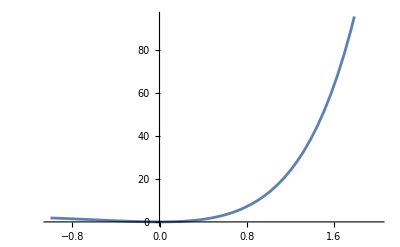

```mathematica
Plot[f[x], {x, -1, 2}]
```

i. Določite intervale konveksnosti in konkavnosti funkcije .

```mathematica
Reduce[f'[x]>0, x]
(*konkavnost*)
Reduce[f'[x]<0, x]
(*konveksnost*)
```

x<-2||x>0

-2<x<0

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [-3, 0]. Vrtenino tudi narišite.

```mathematica
Integrate[2 Pi x(f[x]), {x,-3,0}]
```

10 (-6+78/ⅇ^3) π

```mathematica
RevolutionPlot3D[f[x],{x,-3,0},RevolutionAxis->{1, 0, 0}]
```

-Graphics3D-